# Scratch

Check the eigenvalues of the oscillating part of the mass matrix

```mathematica
Eigenvalues[({{Cos[ζ̂], Sin[ζ̂]}, {Sin[ζ̂], - Cos[ζ̂]}})]
```

{-1,1}

Solution of the same equation where the matrix is constant and diagonal, given by its eigenvalues

```mathematica
DSolve[  {  Ψ''[y]  +  (1 -   η/y^2)Ψ[y]  ==  0  },  Ψ,  y  ]
```

{{Ψ→Function[{y},√y BesselJ[1/2 √(1+4 η),y] C[1]+√y BesselY[1/2 √(1+4 η),y] C[2]]}}

Series expansion of the solutions

```mathematica
Series[  BesselJ[1/2 √(1+4 η),y],  {  y,  0,  1  }  ]
```

y^(1/2 √(1+4 η)) (2^(-1/2 √(1+4 η))/Gamma[1+1/2 √(1+4 η)]+O[y]^2)

```mathematica
Series[  BesselY[1/2 √(1+4 η),y],  {  y,  0,  1 }  ]
```

y^(-1/2 √(1+4 η)) (y^(√(1+4 η)) (-(2^(-1/2 √(1+4 η)) Cos[1/2 π √(1+4 η)] Gamma[-1/2 √(1+4 η)])/π+O[y]^2)+(-(2^(1/2 √(1+4 η)) Gamma[1/2 √(1+4 η)])/π+O[y]^2))

Solution of the same equation, now with “unit” removed, it gives the same asymptotics

```mathematica
DSolve[  {  Ψ''[y]  -   η/y^2 Ψ[y]  ==  0  },  Ψ,  y  ]
```

{{Ψ→Function[{y},y^(1/2 ⅈ (-ⅈ-√(-1-4 η))) C[1]+y^(1/2 ⅈ (-ⅈ+√(-1-4 η))) C[2]]}}

The powers need to be simplified

```mathematica
FullSimplify[1/2 ⅈ (-ⅈ+√(-1-4 η)),  η > 0]
```

1/2 (1-√(1+4 η))

```mathematica
FullSimplify[1/2 ⅈ (-ⅈ-√(-1-4 η)),  η  >  0]
```

1/2 (1+√(1+4 η))

Define the powers of the asymptotic solutions

```mathematica
power1[η_]  :=  Re[  1/2 (1-√(1+4 η))  ]
```

```mathematica
power2[η_]  :=  Re[  1/2 (1+√(1+4 η))  ]
```

Plot the power which is negative for the equation in which the oscillation matrix was removed

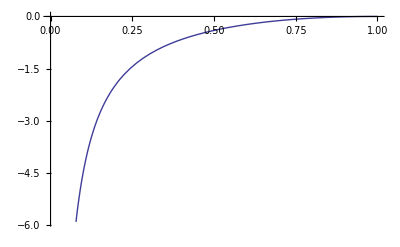

```mathematica
Plot[  power1[  (r - 1/r)^2/4],  {  r,  0,  1  }  ]
```

Find the value of the ratio parameter where the spectrum becomes flat

```mathematica
FindRoot[  power1[  (r - 1/r)^2/4]  +  2,  {  r,  0.25  }  ]
```

{r→0.196262}

Plot the other power

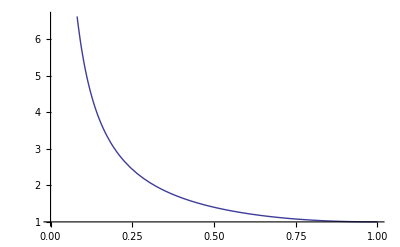

```mathematica
Plot[  power2[  (r - 1/r)^2/4  ],  {  r,  0,  1  }  ]
```

The “eigenvalues” of the total mass matrix

```mathematica
c1[r_]  :=  (r - 1/r)^2/4  +  (r - 1/r)/2 √(r^2  +  1/r^2  +  3)
```

```mathematica
c2[r_]  :=  (r - 1/r)^2/4  -  (r - 1/r)/2 √(r^2  +  1/r^2  +  3)
```

Plot the eigenvalues of the total mass matrix as a function of the ratio parameter

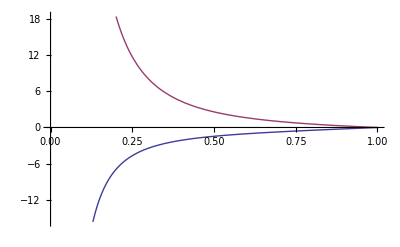

```mathematica
Plot[  {  c1[r],  c2[r]  },  {  r,  0, 1 } ]
```

Plot all the powers of the solutions

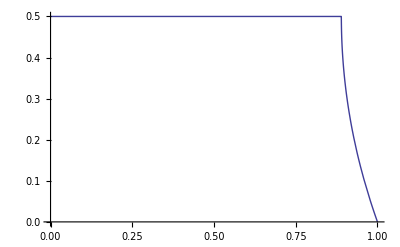

```mathematica
Plot[  power1[  c1[r]  ],  {  r, 0,  1  }  ]
```

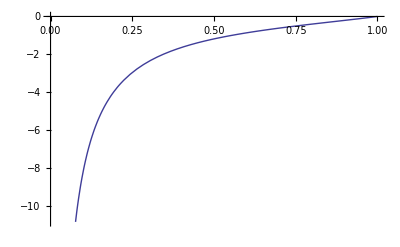

```mathematica
Plot[  power1[  c2[r]  ],  {  r, 0,  1  }  ]
```

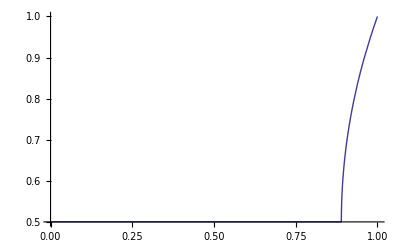

```mathematica
Plot[  power2[  c1[r]  ],  {  r, 0,  1  }  ]
```

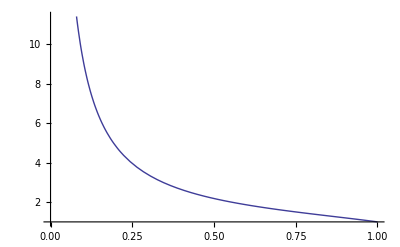

```mathematica
Plot[  power2[  c2[r]  ],  {  r, 0,  1 }  ]
```

The value of the ratio parameter at which one of the powers becomes such that the spectrum is flat

```mathematica
FindRoot[  power1[  c2[r]  ]   +  2,  {  r,  0.5  }  ]
```

{r→0.344025}